{Avg Italian Utility,Avg Swiss Utility,pizza production,pizza consumption,pizza price,fondue production,fondue consumption,fondue price,Swiss hour production,Swiss hour consumption,Swiss hour price,Italian hour production,Italian hour consumption,Italian hour price}

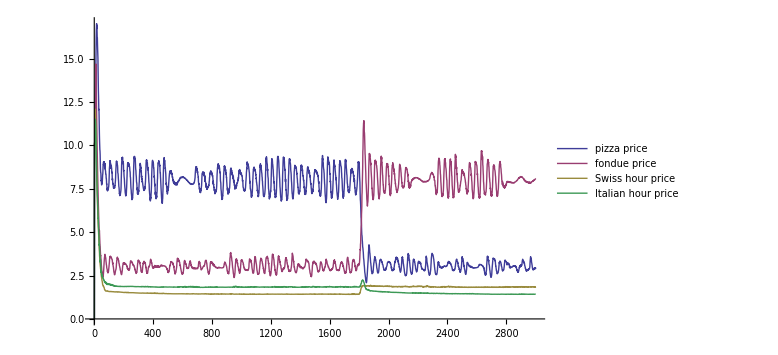

```mathematica
consumerEach = 100;
firmsPerGood = 10;
iterations = 3000;
pizzaPreference = 8;
highProductivity = 6.0;
stockPersistence = 1.0;
smartPriceAdaption = 1; (** 1 or 0 **)

Needs["JLink`"];
ReinstallJava[ClassPath->  NotebookDirectory[] <> "\\..\\bin"];

country = JavaNew["com.abs.World", 24, consumerEach, firmsPerGood, stockPersistence, smartPriceAdaption];
country@updatePreferences[pizzaPreference, pizzaPreference, highProductivity];
country@step[ 1800];
country@updatePreferences[2.0, 2.0, highProductivity];  (**Preference shock **)
country@step[ iterations - 1800];
legend = country@getData[]@getLabels[];
dataT = Transpose[country@getData[]@getAllData[]];

ReleaseJavaObject[country];

legend
selectColumns[data_] := {data[[5]], data[[8]], data[[11]], data[[14]]};
ListLinePlot[selectColumns[dataT], PlotLegends-> selectColumns[legend], PlotRange -> Full, ImageSize->Large]
```